```mathematica
Play[Sin[(t^2+1550t-1500) 2Pi t],{t,0,1}]
```

-Graphics-

```mathematica
Show[{Play[Sin[1000t],{t,0,1}],Play[Sin[2000t],{t,0,1}]}]
```

-Graphics-

```mathematica
Play[FractionalPart[500t],{t,0,1}]
```

-Graphics-

```mathematica
Play[Sign[Sin[1000t]],{t,0,1}]
```

-Graphics-

```mathematica
Play[{t Sin[2000t],(1-t) Sin[2000t]},{t,0,1}]
```

-Graphics-

```mathematica
Play[Evaluate[Table[Sin[t+n Pi/5] Sin[2000t],{n,4}]],{t,0,1}]
```

-Graphics-

```mathematica
Play[Tan[1000t],{t,0,1}]
```

-Graphics-

```mathematica
Play[Tan[1000t],{t,0,1},PlayRange->{0,50}]
```

-Graphics-

```mathematica
Play[Sin[1000t],{t,0,1},SampleRate->1000]
```

-Graphics-

```mathematica
Play[Sin[1000t],{t,0,1},SampleRate->16000]
```

-Graphics-

```mathematica
Play[Sin[1000t]+Sin[1020t],{t,0,2}]
```

-Graphics-

```mathematica
Play[RiemannSiegelZ[1000t],{t,0,1}]
```

-Graphics-

```mathematica
Play[Sum[Sin[1000 Sqrt[n] t],{n,5}],{t,0,1}]
```

-Graphics-

```mathematica
Play[Sum[Sin[1000 Sqrt[n] t(1+Cos[n t])],{n,10}],{t,0,1}]
```

-Graphics-

```mathematica
Play[Sum[Sin[2000 2^t n t],{n,5}],{t,0,4}]
```

-Graphics-

```mathematica
Play[(2+Cos[40t])Sin[2000t],{t,0,1}]
```

-Graphics-

```mathematica
Sound[{Play[Cos[50t]Sin[3000t],{t,0,1}],SoundNote[]}]
```

-Graphics-

```mathematica
Sound[{Sound[Play[Cos[50t]Sin[4000t],{t,0,1}],{0,1}],Sound[SoundNote[],{0,1}]}]
```

-Graphics-

```mathematica
Play[Sin[100000t],{t,0,1}]
```

-Graphics-

```mathematica
Play[Sin[2π 20000 t],{t,0,2}]
```

-Graphics-

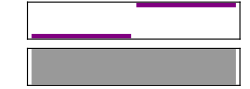

```mathematica
Sound[{SoundNote["C"],SoundNote["G"]}]
```

```mathematica
Sound[{Play[Sin[1000t(1+t^2)],{t,0,.2}],Play[Sin[500t (1+t^3)],{t,0,.5}]}]
```

-Graphics-

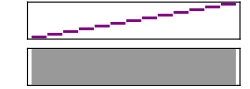

```mathematica
Sound[Table[SoundNote[i],{i,0,12}]]
```

```mathematica
Sound[Table[SoundNote[i],{i,0,12}],1.5]
```

-Graphics-

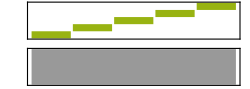

```mathematica
Sound[{"Accordion",Table[SoundNote[i],{i,5}]}]
```

```mathematica
s=Sound[Table[SoundNote[i],{i,0,12}],1]
```

-Graphics-

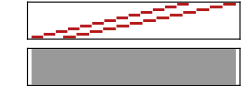

```mathematica
Sound[{"Flute",Sound[s,{0,1}],"Trumpet",Sound[s,{.2,1.3}]}]
```

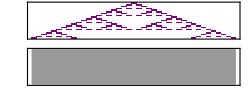

```mathematica
Sound[SoundNote[DeleteCases[3 Range[21]Reverse[#],0]-24,.1]&/@Transpose[CellularAutomaton[90,{{1},0},20]]]
```

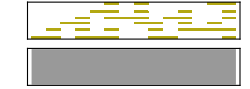

```mathematica
Sound[SoundNote[#,1/6,"Warm"]&/@(Pick[{0,5,9,12,16,21},#,1]&/@CellularAutomaton[30,{{1,0,0,0,0,0},0},13,{13,5}])]
```

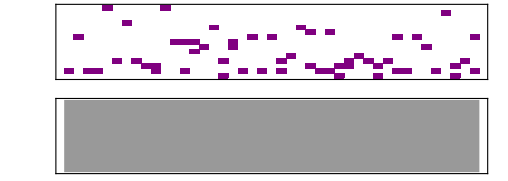

```mathematica
Sound[SoundNote[#,1,RandomChoice[{"Piano"}]]& /@ {1,8,1,1,14,3,11,3,2,{2,1},14,{7,7},{7,1},{7,5},6,10,{0,3},{6,7},1,8,1,8,{1,3},4,10,{2,9},1,{1,9},{0,2},{2,3},4,{3,3},{0,2},3,{1,8},{1,1},8,6,{1,1},13,{0,2},3,{1,8}},12]
```

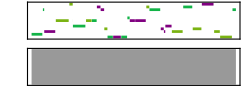

```mathematica
Sound[SoundNote[#,RandomReal[2],RandomChoice[{"Piano","Cello","Tuba"}]]& /@ RandomInteger[12, 30], 4]
```

```mathematica
note[b_,x0_,t_,v_]:=(a=b;
Which[x0=="1",Append[a,SoundNote["C",t,SoundVolume->v]],x0=="2",Append[a,SoundNote["D",t,SoundVolume->v]],x0=="3",Append[a,SoundNote["E",t,SoundVolume->v]],x0=="4",Append[a,SoundNote["F",t,SoundVolume->v]],x0=="5",Append[a,SoundNote["G",t,SoundVolume->v]],x0=="6",Append[a,SoundNote["A",t,SoundVolume->v]],x0=="7",Append[a,SoundNote["B",t,SoundVolume->v]],x0=="0",Append[a,SoundNote[None,t,SoundVolume->v]],x0=="-",(k=SoundNote[First[Last[a]],Part[Last[a],2]+t,SoundVolume->v];aa=Drop[a,-1];a=Append[aa,k]),x0=="_",(k=SoundNote[First[Last[a]],Part[Last[a],2]/2,SoundVolume->v];
aa=Drop[a,-1];a=Append[aa,k]),x0=="*",(k=SoundNote[First[Last[a]],Part[Last[a],2]*1.5,SoundVolume->v];aa=Drop[a,-1];a=Append[aa,k]),x0=="t",(k=SoundNote[First[Last[a]],Part[Last[a],2]/3,SoundVolume->v];
aa=Drop[a,-1];a=Append[aa,k]),x0==".",(k=SoundNote[StringInsert[First[Last[a]],"3",-1],Part[Last[a],2],SoundVolume->v];aa=Drop[a,-1];
a=Append[aa,k]),x0=="'",(k=SoundNote[StringInsert[First[Last[a]],"5",-1],Part[Last[a],2],SoundVolume->v];aa=Drop[a,-1];
a=Append[aa,k]),x0=="#",(k=SoundNote[StringInsert[First[Last[a]],"#",-1],Part[Last[a],2],SoundVolume->v];aa=Drop[a,-1];
a=Append[aa,k]),x0=="b",(k=SoundNote[StringInsert[First[Last[a]],"b",-1],Part[Last[a],2],SoundVolume->v];aa=Drop[a,-1];
a=Append[aa,k]),True,a]);
mf[s_,t_,x_]:=(lh=StringLength[x];xx=x;a={};v=1;
For[i=1,i≤lh,i++,x0=StringTake[xx,1];
v=Which[x0=="p",0.5,x0=="P",0.2,x0=="m",0.8,x0=="f",1,True,v];a=note[a,x0,t,v];
xx=StringDrop[xx,1]];Sound[Prepend[a,s]]);
(*函数mf[s,t,x]，s，t，x分别为乐器类型、时长单位 （秒）、乐谱*)
m[t_,x_]:=mf["Piano",t,x];
(*函数m[t,x]，t，x分别为每一拍子的时长 （秒）、乐谱，乐器类型默认为钢琴*)
ms[s_,x_]:=mf[s,0.4,x];
(*函数ms[s,x]，s，x分别为乐器类型、乐谱，时长单位默认为0 .4秒*)
m0[x_]:=m[0.4,x];
(*函数m0[x]，x为乐谱，乐器类型默认为钢琴，时长单位默认为0 .4秒*)
```

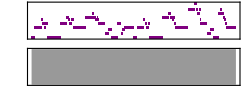

```mathematica
m[0.5,"5.|1*1_3_2_1_2__2__|5.-5.5.|2*2_4_3_2_3__3__|1-11|4*4_5_4_3_4__3__|2-6.7.|5.*5._2_2_6._7.__7.__|1-15.|1*1_3_2_1_2__2__|5.-5.5.|4*4_5_4_3_4__2__|1-11|6*6_1'_6_5_6__3__|2-6.7.|5.*5_6_5_4_3__2__|1-1"]
```

```mathematica
m[0.3,  "5.|11_1_22|32_1_54_5._|11_1_22|32_1_6*5_|43_2_12|6.-0p5.|11_1_22|32_\

1_54_5._|11_1_22|32_1_6*5_|43_2_12|6.-0m5.|11_1_22|32_1_54_5._|11_1_\

22|32_1_6*5_|43_2_12|6.-0f5.|11_1_22|32_1_54_5._|11_1_22|32_1_6*5_|43_\

2_12|6.-05.|11_1_22|32_1_54_5._|11_1_22|32_1_6*5_|43_2_12|6_-"]
```

```mathematica
{Height,Width,Mines}=DialogInput[{height=10,width=10,mines=10},Column[{Row[{"高　　",InputField[Dynamic[height],Number]}],Row[{"宽　　",InputField[Dynamic[width],Number]}],Row[{"地雷数",InputField[Dynamic[mines],Number]}],Button["确定",If[IntegerQ[height]&&IntegerQ[width]&&IntegerQ[mines]&&height>0&&height*width>mines>0,DialogReturn[{height,width,mines}]],ImageSize->Automatic]}]];

Reset[]:=(MineArray=ConstantArray[0,{Height,Width}];
DisplayArray=ConstantArray[" ",{Height,Width}];
PressedArray=ConstantArray["DialogBox",{Height,Width}];
MinesRemain=Mines;Smiley="😐";State="挖";
For[n=1,n≤Mines,n++,p=RandomChoice[Position[MineArray,0]];
MineArray[[p[[1]],p[[2]]]]=1]);

Dig[i_,j_]:=(If[DisplayArray[[i,j]]===" ",DisplayArray[[i,j]]=Style[Plus@@(MineArray[[i+#[[1]],j+#[[2]]]]&/@Module[{temp={{-1,-1},{0,-1},{1,-1},{-1,0},{1,0},{-1,1},{0,1},{1,1}}},If[i==1,temp=Cases[temp,Except[{-1,_}]]];
If[i==Height,temp=Cases[temp,Except[{1,_}]]];
If[j==1,temp=Cases[temp,Except[{_,-1}]]];
If[j==Width,temp=Cases[temp,Except[{_,1}]]];temp]),23];PressedArray[[i,j]]="Pressed";
If[DisplayArray[[i,j]]===Style[0,23],DisplayArray[[i,j]]="";
Dig[i+#[[1]],j+#[[2]]]&/@Module[{temp={{-1,-1},{0,-1},{1,-1},{-1,0},{1,0},{-1,1},{0,1},{1,1}}},If[i==1,temp=Cases[temp,Except[{-1,_}]]];
If[i==Height,temp=Cases[temp,Except[{1,_}]]];
If[j==1,temp=Cases[temp,Except[{_,-1}]]];
If[j==Width,temp=Cases[temp,Except[{_,1}]]];temp]];]);

Win[]:=If[Position[DisplayArray," "]=={}&&MinesRemain==0,Smiley="☺";Speak["you win"]];

CreateDialog[Reset[];
Deploy[Panel[Column[{Row[{Dynamic[Style[MinesRemain,15]],"        ",Button[Dynamic[Style[Smiley,25]],Reset[],ImageSize->{25,26}]}],RadioButtonBar[Dynamic[State],{"挖","标"}],Grid[Table[With[{i=i,j=j},Button[Dynamic[DisplayArray[[i,j]]],If[Smiley=="😐",If[State=="标",If[DisplayArray[[i,j]]===" ",DisplayArray[[i,j]]=Style["𝔉",25];
MinesRemain--,If[DisplayArray[[i,j]]===Style["𝔉",25],DisplayArray[[i,j]]=" ";MinesRemain++]];Win[],If[MineArray[[i,j]]==1&&DisplayArray[[i,j]]===" ",Smiley="☹";Speak["you lost"];
DisplayArray=Table[If[DisplayArray[[k,l]]===Style["𝔉",25],If[MineArray[[k,l]]==0,Style["×",23],Style["𝔉",25]],If[MineArray[[k,l]]==1,Style["\[KernelIcon]",17],DisplayArray[[k,l]]]],{k,1,Height},{l,1,Width}];
PressedArray=Table[If[DisplayArray[[k,l]]===Style["×",23]||DisplayArray[[k,l]]===Style["\[KernelIcon]",17],"Pressed",PressedArray[[k,l]]],{k,1,Height},{l,1,Width}],Dig[i,j];Win[]]]],ImageSize->{25,25},Appearance->Dynamic[PressedArray[[i,j]]]]],{i,1,Height},{j,1,Width}],Spacings->{0,0}]}]]]]
```

```mathematica
{Height,Width,Speed}=DialogInput[{height=23,width=13,speed=1.4},Column[{Row[{"Height",InputField[Dynamic[height],Number]}],Row[{"Width ",InputField[Dynamic[width],Number]}],Row[{"Speed ",InputField[Dynamic[speed],Number]}],Button["OK",If[IntegerQ[height]&&IntegerQ[width]&&height>0&&width>0&&speed>0,DialogReturn[{height,width,speed}]],ImageSize->Automatic]}]]

TetrisPlot[array_]:=Graphics[{EdgeForm[Black],Gray,Rectangle/@Position[array,1]},PlotRange->({1,1+#}&)/@Dimensions@array,ImageSize->20 Dimensions@array,Frame->True,FrameTicks->None];

ClearLine[array_,n_]:=Join[array[[;;n-1]],array[[n+1;;]],{Table[0,{Dimensions[array][[2]]}]}];

ShowTetromino[n_]:=Switch[n,0,{{1,1,0,0},{0,1,1,0}},1,{{0,1,1,0},{1,1,0,0}},2,{{1,1,1,0},{1,0,0,0}},3,{{1,0,0,0},{1,1,1,0}},4,{{1,1,1,1},{0,0,0,0}},5,{{1,1,0,0},{1,1,0,0}},6,{{1,1,1,0},{0,1,0,0}}];

RestartTetris2[]:=(Tetris2[[-4;;,Floor[Dimensions[Tetris2][[2]]/2];;Floor[Dimensions[Tetris2][[2]]/2]+1]]=Transpose@ShowTetromino[Tetromino];Tetromino=RandomInteger[6];);

CreateDialog[RemoveScheduledTask[ScheduledTasks[]];
Tetromino=RandomInteger[6];
Pausing=True;
Stop=True;
Score=0;
Tetris1=Table[0,{Height},{Width}];
Tetris2=Table[0,{Height+4},{Width}];
RestartTetris2[];
RunScheduledTask[If[!Pausing,Module[{i},If[Max[Tetris1[[-1]]]==1,Pausing=Stop=True;
CreateDialog[{TextCell["Game over."],Row@{"Score:",Score},DefaultButton[]}],If[Max[Tetris1+RotateLeft[Tetris2][[;;-5]]]>1||Max[Tetris2[[1]]]==1,Tetris1=Tetris1+Tetris2[[;;-5]];
Tetris2=Table[0,{Dimensions[Tetris2][[1]]},{Dimensions[Tetris2][[2]]}];RestartTetris2[],Tetris2=RotateLeft@Tetris2];
For[i=Length@Tetris1,i>0,i--,If[Min[Tetris1[[i]]]==1,Tetris1=ClearLine[Tetris1,i];
Score++]]]]],1./Speed];
Panel[Row@{Deploy@Dynamic[TetrisPlot[Transpose[Plus@@{Tetris1,Tetris2[[;;-5]]}]]],Column@{Row@{"Score:",Dynamic[Score]},Deploy@Dynamic[TetrisPlot[ShowTetromino@Tetromino]],Button[Dynamic[If[Stop,"Start","Restart"]],Stop=Pausing=False;Score=0;
Tetris1=Table[0,{Height},{Width}];
Tetris2=Table[0,{Height+4},{Width}];RestartTetris2[]],Button[Dynamic[If[Pausing,"Resume","Pause"]],If[Pausing,Pausing=False,Pausing=True],Enabled->Dynamic[!Stop]],Button["↑",Tetris2=Module[{temp},temp=RotateRight[Reverse@Transpose@RotateLeft[PadRight[Tetris2,{Max@Dimensions@Tetris2,Max@Dimensions@Tetris2}],Floor@Mean@Position[Tetris2,1]],Floor@Mean@Position[Tetris2,1]][[;;Dimensions[Tetris2][[1]], ;;Dimensions[Tetris2][[2]]]];
If[Length@Position[temp,1]==4&&Max[temp[[;;-5]]+Tetris1]≤1,temp,Tetris2]],Enabled->Dynamic[!Pausing]],Button["←",If[Max[Tetris2[[All,1]]]==0,Tetris2=Module[{temp},temp=RotateLeft[Tetris2,{0,1}];
If[Max[temp[[;;-5]]+Tetris1]≤1,temp,Tetris2]]],Enabled->Dynamic[!Pausing]],Button["→",If[Max[Tetris2[[All,-1]]]==0,Tetris2=Module[{temp},temp=RotateLeft[Tetris2,{0,-1}];
If[Max[temp[[;;-5]]+Tetris1]≤1,temp,Tetris2]]],Enabled->Dynamic[!Pausing]],Dynamic[If[Stop,"Stop",If[Pausing,"Pausing","Playing"]]]}}]]
```

```mathematica
DynamicModule[{array=Table[RandomChoice[{1,0}],{i,1,20},{j,1,20}],k=20,Going=False,map="torus",GoNext},GoNext[array_,k_,map_]:=Module[{ip,jp,in,jn,temp},Switch[map,"torus",Table[(ip=If[i==1,-1,i-1];
jp=If[j==1,-1,j-1];
in=If[i==k,1,i+1];
jn=If[j==k,1,j+1];
temp=array[[ip,jp]]+array[[i,jp]]+array[[in,jp]]+array[[ip,j]]+array[[in,j]]+array[[ip,jn]]+array[[i,jn]]+array[[in,jn]];
Switch[temp,2,array[[i,j]],3,1,_,0]),{i,1,k},{j,1,k}],"cylinder",Table[(ip=If[i==1,-1,i-1];
jp=If[j==1,-1,j-1];
in=If[i==k,1,i+1];
jn=If[j==k,1,j+1];
temp=If[i==1||i==k,0,array[[ip,jp]]+array[[i,jp]]+array[[in,jp]]+array[[ip,j]]+array[[in,j]]+array[[ip,jn]]+array[[i,jn]]+array[[in,jn]]];
Switch[temp,2,array[[i,j]],3,1,_,0]),{i,1,k},{j,1,k}],"square",Table[(ip=If[i==1,-1,i-1];
jp=If[j==1,-1,j-1];
in=If[i==k,1,i+1];
jn=If[j==k,1,j+1];
temp=If[i==1||i==k||j==1||j==k,0,array[[ip,jp]]+array[[i,jp]]+array[[in,jp]]+array[[ip,j]]+array[[in,j]]+array[[ip,jn]]+array[[i,jn]]+array[[in,jn]]];
Switch[temp,2,array[[i,j]],3,1,_,0]),{i,1,k},{j,1,k}]]];Panel[Row[{Column[{Row[{"Map:",PopupMenu[Dynamic[map],{"torus","cylinder","square"}]}],Row[{"Size:",Dynamic[k],Slider[Dynamic[k],{10,100,1}]}," "],Row[{"Control:",Button["Go",Going=True],Button["Stop",Going=False],Button["Reset",array=Table[RandomChoice[{1,0}],{i,1,k},{j,1,k}]],Button["GoNext",array=GoNext[array,k,map]]}," "],Column[Table["",{i,1,27}]],Dynamic[If[Going,"Going","Stop"]]}] Panel[Deploy[Dynamic[ArrayPlot[If[Going,array=GoNext[array,k,map],array],Mesh->All,MeshStyle->White,ImageSize->500]]]]}]]]
```

```mathematica
Table[ArrayPlot[Table[(z=x+y I;n=1;
While[n<30&&Abs[z]<5,z=z^2+k (x+y I);n++];
n),{x,-2,2,0.01},{y,-2,2,0.01}]],{k,0,2,0.1}];

Export["D:\\mov1.gif",%];
```

```mathematica
DensityPlot[Block[{z,t=0},z=x+y*I;While[(Abs[z]<2.0)&&(t<100),++t;z=z^2+x+y*I];Return[t]],{x,-2,0.8},{y,-1.5,1.5},PlotPoints->200]
```

```mathematica
ListPlot3D[Table[If[Mod[Binomial[n,k],2]==1,1,0],{n,0,128},{k,0,128}]]
```